```mathematica
Clear[x,fx1,fx2,fx3,pfx1,pfx2,pfx3]
```

Problem 1

2.b.

Define the pdfs as function.

```mathematica
fx1[x_]:=1/(√(2*Pi)2)E^((-(x-4)^2)/(2*2^2))
 fx2[x_]:=1/(√(2*Pi)3)E^((-(x-6)^2)/(2*3^2))
fx3[x_]:=1/(√(2*Pi)2)E^((-(x-5)^2)/(2*2^2))
```

Solve for the intersection between each of the decision regions

```mathematica
NSolve[fx2[x]==fx1[x],x]
NSolve[fx3[x]==fx1[x],x]
NSolve[fx3[x]==fx2[x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.00569},{x→5.80569}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→4.5}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.50209},{x→6.89791}}

Region 2 is bounded between x=-∞ and x=-1.00569.

Region 1 is bounded between x=-1.00569 and x=4.5.

Region 3 is bounded between x=4.5 and x=6.89791.

Region 2 is bounded between x=6.89791 and x=∞.

2.c.

Since there are four separate decision regions, and each decision region has two elements of error, there are eight total elements to the overall error for the decision model. Region 2 has error  for misclassifying ω_1 and ω_3, Region 1 has error for misclassifying ω_2 and ω_3, Region 3 has error for misclassifying ω_1 and ω_2, and again Region 2 has error  for misclassifying ω_1 and ω_3. The overall error for the decision model is the summation of the eight different elements of error.

```mathematica
∫_(-∞)^-1.00569 fx1[x]*1/3 ⅆx+∫_(-∞)^-1.00569 fx3[x]*1/3 ⅆx+∫_-1.00569^4.5 fx2[x]*1/3 ⅆx+∫_-1.00569^4.5 fx3[x]*1/3 ⅆx+∫_4.5^6.89791 fx1[x]*1/3 ⅆx+∫_4.5^6.89791 fx2[x]*1/3 ⅆx+∫_6.89791^∞ fx1[x]*1/3 ⅆx+∫_6.89791^∞ fx3[x]*1/3 ⅆx
```

0.529316

The overall error for the decision model is 52.93% chance of misclassifying.

3.a.

Define the posterior probabilities incorporating the prior probabilities and the normalization factor. Then plot.

```mathematica
pfx1[x_]:=(fx1[x]*.6)/(fx1[x]*.6+fx2[x]*.2+fx3[x]*.2)
pfx2[x_]:=(fx2[x]*.2)/(fx1[x]*.6+fx2[x]*.2+fx3[x]*.2)
pfx3[x_]:=(fx3[x]*.2)/(fx1[x]*.6+fx2[x]*.2+fx3[x]*.2)
```

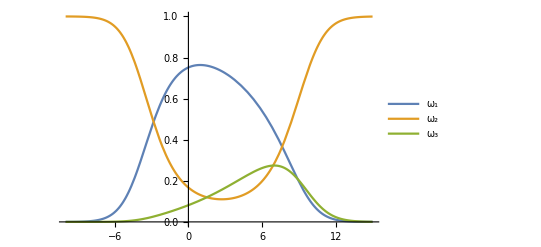

```mathematica
Plot[{pfx1[x],pfx2[x],pfx3[x]},{x,-10,15},PlotLegends->{"ω_1","ω_2","ω_3"}]
```

3.b.

With the prior probabilities no longer being equal, we no longer have four decision regions, it has been reduced to three regions. Visually, you can see that x=4.7 will fall into Decision Region 1, however, we will solve for the analytical endpoints of the region to make sure. Again looking visually, you can see that ω_3 is dominated throughout the decision model.

```mathematica
NSolve[pfx2[x]==pfx1[x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2.83629},{x→7.63629}}

Region 1 is bounded between x=-2.83629 and x=7.63629. So, x=4.7 falls within this region and hence would be classified as ω_1.

Problem 2

1. Plot both class 1 and class 2 pdfs on a single graph.

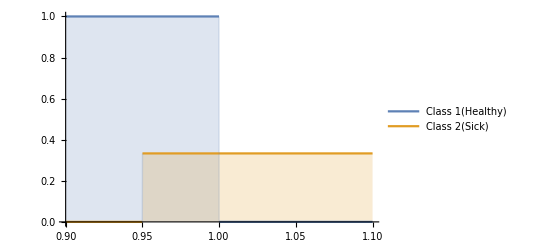

```mathematica
Plot[{PDF[UniformDistribution[{0,1}],x],PDF[UniformDistribution[{0.95,3.95}],x]}//Evaluate,{x,.9,1.1},Filling->Axis,PlotLegends->{"Class 1(Healthy)","Class 2(Sick)"}]
```

2. Equal prior probabilities and a decision boundary of x=0.97.

2.a. A false negative will occur when the patient is sick, but is classified as healthy. With a decision boundary of x=.97, the probability of a false negative is given by the integral of class 2 from x=0.95 to x=0.97.

```mathematica
u2[x_]:=(1/(3.95-.95)*.5)/(1/(3.95-.95)*.5+1/1*.5)
∫_(.95)^(.97) u2[x]*.5ⅆx
```

0.0025

Based upon a decision boundary of x=0.97, the model would classify a sick person as healthy 0.25% of the time.

2.b. A false positive will occur when the patient is healthy, but is classified as sick. With a decision boundary of x=.97, the probability of a false positive is given by the integral of class 1 from x=0.97 to x=1.

```mathematica
u1[x_]:=(1/1*.5)/(1/(3.95-.95)*.5+1/1*.5)
∫_(.97)^1 u1[x]*.5ⅆx
```

0.01125

Based upon a decision boundary of x=0.97, the model would classify a healthy person as sick 0.25% of the time.

3.

Define overall error as a function of a which is a variable decision boundary point. Moving a in between the two boundary end points will adjust the decision model overall error.

```mathematica
error[a_]:=∫_a^1 u1[x]*.5ⅆx+∫_(.95)^a u2[x]*.5ⅆx
error[a]
```

0.375 (1-a)+0.125 (-0.95+a)

error[a] is a line with a negative slope. Usual optimization would require taking the derivative of the function and and setting it equal to zero to identify the mins/maxs of the error function. Since it is a line, the derivative in this case will result in a negative constant which isn’t helpful. Checking the end points of the function within the domain of a=.95 to a=1 will provide either a max of the function or a min.

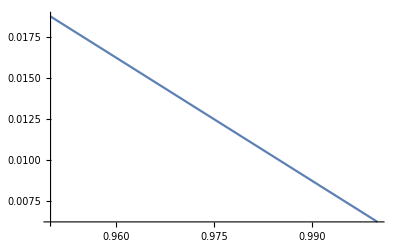

```mathematica
Plot[error[a], {a,.95,1.0}]
```

```mathematica
error[.95]
error[1]
```

0.01875

0.00625

The optimized value for the decision point is a=1 which is in line with Bayes Decision Theory as ω_1 dominates ω_2 from x=0 to x=1 and then switches to ω_2 being the dominant decision rule.

Changing the prior probabilities can be accomplished in the same way, except we will expand the function to include k and will replace the prior probability in ω_1 and (1-k) will replace it in ω_2.

```mathematica
error[a_,k_]:=∫_a^1 u1[x]*kⅆx+∫_(.95)^a u2[x]*(1-k)ⅆx
```

```mathematica
Plot3D[error[a,k],{a,.95,1},{k,0,1}]
```

-Graphics3D-

There are no obvious local optimal points. We then check the four corners of the answer space (.95,0), (.95,1), (1,0), and (1,1).

```mathematica
error[.95,0]
error[.95,1]
error[1,0]
error[1,1]
```

0.

0.0375

0.0125

0.

Error is minimized in two cases:

The decision boundary is .95 and we assume everyone has the disease.

The decision boundary is 1 and we assume no one has the disease.

Both of these cases require the ignorance of reality to achieve 0% chance of error. We know that there are both people with and without the disease, but, in order to achieve 0% error, we assume the prior probability of the classification that results in error is in effect 0.0.